```mathematica
Clear[w,wo,ux,b2];
w=1;
wo=1;
ux[γ_,ξ_,nx_,nz_]:=1/((γ^2*(1+ξ)^2)/(w*wo)+(nz-nx)/wo);
b2[γ_,ξ_,nx_,nz_]:=1/2*(1-ux[γ,ξ,nx,nz]);
a2[γ_,ξ_,nx_,nz_]:=(γ^2*(1+ξ)^2)/(4*w)*(1-ux[γ,ξ,nx,nz]^2);
```

```mathematica
Clear[d,γ2,tb2,tb2x];
d=0.001;
γ2=2;
tb2[ξ_,nx_,nz_]:=Table[{γ,b2[γ,ξ,nx,nz]},{γ,0,γ2,d}]
(*Raíces en x*)
Clear[rtb2,tb2x]
rtb2[ξ_,nx_,nz_]:=γ/.Solve[b2[γ,ξ,nx,nz]==0,γ];
tb2x[ξ_,nx_,nz_]:=Table[{γ,b2[γ,ξ,nx,nz]},{γ,rtb2[ξ,nx,nz][[2]],γ2,d}]
(*Gráficas*)
pb2[ξ_,limite_,xc_,yc_]:=ListPlot[{tb2[ξ,0,0],tb2x[ξ,0.1,0],tb2x[ξ,0.5,0],tb2x[ξ,0.9,0],tb2x[ξ,0,0.1],tb2x[ξ,0,0.5],tb2x[ξ,0,0.9]},
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,γ2},{0,0.5}},
FrameLabel->{Style["γ",FontSize->25,xc],Style["β^2",FontSize->25,yc]},
FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
PlotLabel->Style[Row[{limite ," (ξ = ",ξ, ")"}],Bold,25,Black],
PlotStyle->{RGBColor[0.3,0.3,0.3],RGBColor[0.2,0.4,0.8],RGBColor[0.5,0.2,0.6],RGBColor[0.8,0.4,0.2],RGBColor[0.8,0.2,0.4],RGBColor[0.4,0.6,0.8],RGBColor[0.2,0.8,0.4]},
(*PlotLegends->{"η_x=0, η_y=0, η_z=0","η_x=0.9, η_y=0, η_z=0","η_x=0, η_y=0, η_z=0.9"},*)
ImageSize->600];
```

```mathematica
Clear[d,γ2,ta2];
d=0.001;
γ2=2;
ta2[ξ_,nx_,nz_]:=Table[{γ,a2[γ,ξ,nx,nz]},{γ,0,γ2,d}];
(*Gráficas*)
Clear[pa2]
pa2[ξ_,limite_,xc_,yc_]:=ListPlot[{ta2[ξ,0,0],ta2[ξ,0.1,0],ta2[ξ,0.5,0],ta2[ξ,0.9,0],ta2[ξ,0,0.1],ta2[ξ,0,0.5],ta2[ξ,0,0.9]},
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,γ2},{0,1}},
FrameLabel->{Style["γ",FontSize->25,xc],Style["α^2",FontSize->25,yc]},
FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},None},{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
PlotStyle->{RGBColor[0.3,0.3,0.3],RGBColor[0.2,0.4,0.8],RGBColor[0.5,0.2,0.6],RGBColor[0.8,0.4,0.2],RGBColor[0.8,0.2,0.4],RGBColor[0.4,0.6,0.8],RGBColor[0.2,0.8,0.4]},
(*PlotLegends->{"η_x=0, η_y=0, η_z=0","η_x=0.9, η_y=0, η_z=0","η_x=0, η_y=0, η_z=0.9"},*)
ImageSize->600];
```

```mathematica
Clear[En,Es]
(*Funciones*)
En[nz_]:=1/4*(nz-2*wo);
Es[γ_,ξ_,nx_,nz_]:=-1/4*(wo/ux[γ,ξ,nx,nz]*(1+ux[γ,ξ,nx,nz]^2)-nz);
Clear[d,γc]
d=0.0001;
γc[ξ_,nx_,nz_]:=Sqrt[(w*wo)/(1+ξ)^2*(1-(nz-nx)/wo)];
(*Tablas *)
Clear[tEn,tEs]
tEn[ξ_,nx_,nz_]:=Table[{γ,En[nz]},{γ,0,γc[ξ,nx,nz],d}];
tEs[ξ_,nx_,nz_]:=Table[{γ,Es[γ,ξ,nx,nz]},{γ,γc[ξ,nx,nz],2,d}];
(*Graficas*)
Clear[pE]
pE[ξ_,xc_,yc_]:=ListPlot[{tEn[ξ,0,0],tEn[ξ,0.1,0],tEn[ξ,0.5,0],tEn[ξ,0.9,0],tEn[ξ,0,0.1],tEn[ξ,0,0.5],tEn[ξ,0,0.9],tEs[ξ,0,0],tEs[ξ,0.1,0],tEs[ξ,0.5,0],tEs[ξ,0.9,0],tEs[ξ,0,0.1],tEs[ξ,0,0.5],tEs[ξ,0,0.9]},
PlotRange->{{0,2},{-2,0}},
Joined->True,
Mesh->All,
Frame->True,
FrameLabel->{Style["γ",FontSize->25,xc],Style["E_0/N",FontSize->25,yc]},
FrameTicks->{{{-2,-1.8,-1.6,-1.4,-1.2,-1,-0.8,-0.6,-0.4,-0.2,0},None},{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8,2},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
PlotStyle->{RGBColor[0.3,0.3,0.3],RGBColor[0.2,0.4,0.8],RGBColor[0.5,0.2,0.6],RGBColor[0.8,0.4,0.2],RGBColor[0.8,0.2,0.4],RGBColor[0.4,0.6,0.8],RGBColor[0.2,0.8,0.4]},
(*PlotLegends->{"η_x=0, η_y=0, η_z=0","η_x=0.9, η_y=0, η_z=0","η_x=0, η_y=0, η_z=0.9"},*)
ImageSize->600];
```

```mathematica
Clear[d,γ12,t1a2];
a12[γ_,ξ_,nx_,nz_]:=2*Pi*(γ^2*(1+ξ)^2)/(4*w)*(1-ux[γ,ξ,nx,nz]^2);
d=0.001;
γ12=2;
t1a2[ξ_,nx_,nz_]:=Table[{γ,a12[γ,ξ,nx,nz]},{γ,0,γ2,d}];
(*Gráficas*)
Clear[p1a2]
p1a2[ξ_,limite_,xc_,yc_]:=ListPlot[{t1a2[ξ,0,0],t1a2[ξ,0.1,0],t1a2[ξ,0.5,0],t1a2[ξ,0.9,0],t1a2[ξ,0,0.1],t1a2[ξ,0,0.5],t1a2[ξ,0,0.9]},
Joined->True,
Mesh->All,
Frame->True,
PlotRange->{{0,1.8},{0,6}},
FrameLabel->{Style["γ",FontSize->25,xc],Style["γ_0",FontSize->25,yc]},
FrameTicks->{{{0,1,2,3,4,5,6},None},{{0,0.2,0.4,0.6,0.8,1,1.2,1.4,1.6,1.8},None}},
FrameTicksStyle->Directive[FontSize->14,Black],
PlotStyle->{RGBColor[0.3,0.3,0.3],RGBColor[0.2,0.4,0.8],RGBColor[0.5,0.2,0.6],RGBColor[0.8,0.4,0.2],RGBColor[0.8,0.2,0.4],RGBColor[0.4,0.6,0.8],RGBColor[0.2,0.8,0.4]},
(*PlotLegends->{"η_x=0, η_y=0, η_z=0","η_x=0.9, η_y=0, η_z=0","η_x=0, η_y=0, η_z=0.9"},*)
ImageSize->600];
```

Power::infy: Infinite expression 1/0. encountered.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

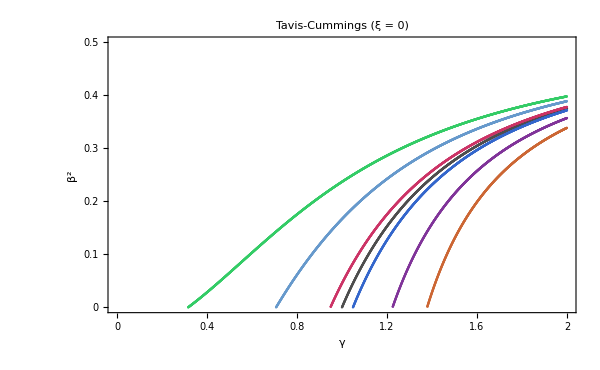
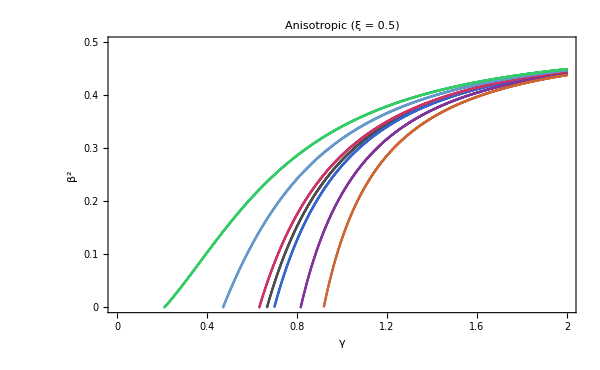
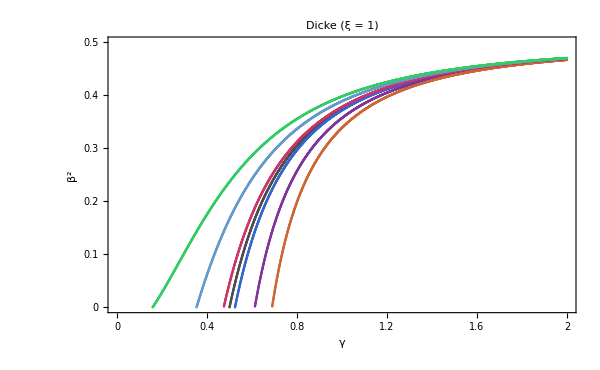
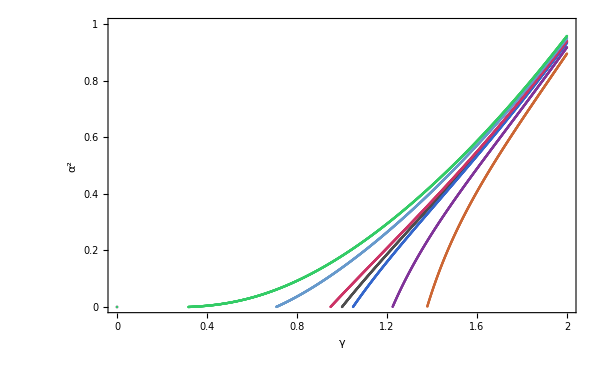
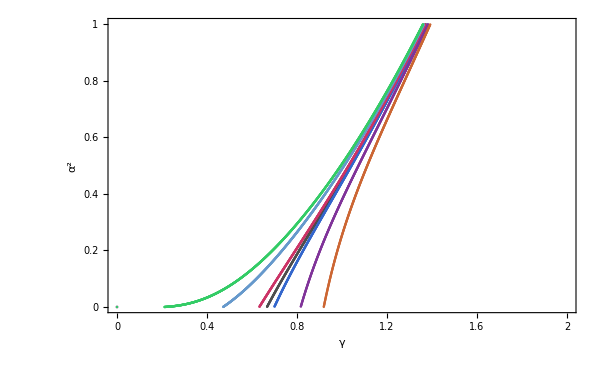
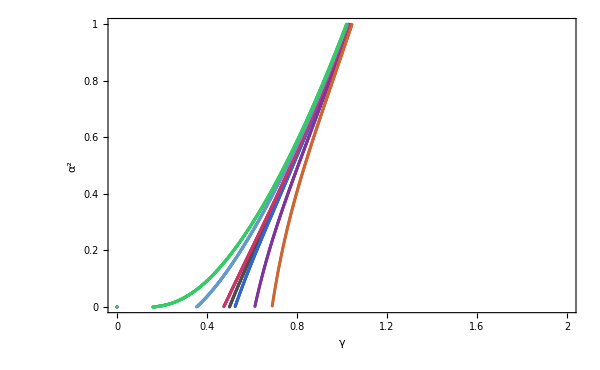
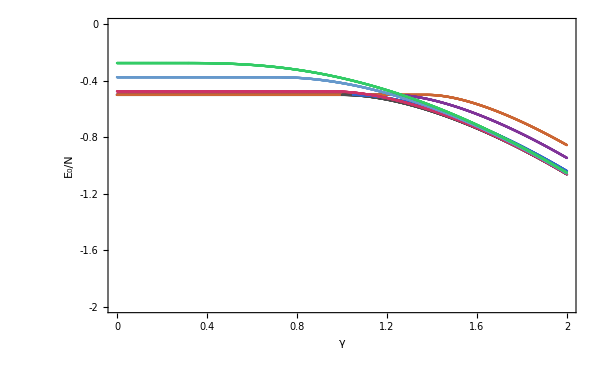
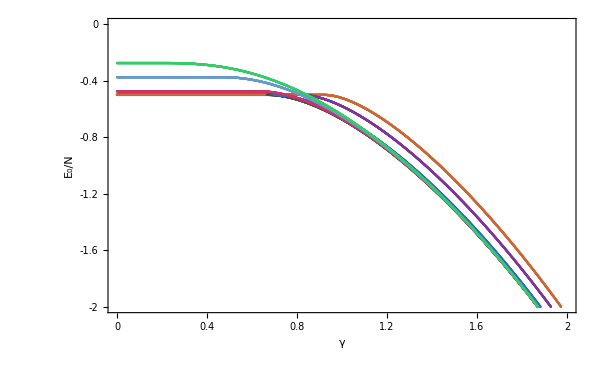
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
 |  |  |  |  |  |  |  |

```mathematica
Clear[legend1,legend2,legend3]
legend1=LineLegend[{Directive[RGBColor[0.3,0.3,0.3],AbsoluteThickness[4]]},{"η_x=0,η_z=0"},LegendMarkerSize->{40,20}];
legend2=LineLegend[{Directive[RGBColor[0.2,0.4,0.8],AbsoluteThickness[4]]},{"η_x=0.1,η_z=0"},LegendMarkerSize->{40,20}];
legend3=LineLegend[{Directive[RGBColor[0.5,0.2,0.6],AbsoluteThickness[4]]},{"η_x=0.5,η_z=0"},LegendMarkerSize->{40,20}];
legend4=LineLegend[{Directive[RGBColor[0.8,0.4,0.2],AbsoluteThickness[4]]},{"η_x=0.9,η_z=0"},LegendMarkerSize->{40,20}];
legend5=LineLegend[{Directive[RGBColor[0.8,0.2,0.5],AbsoluteThickness[4]]},{"η_x=0,η_z=0.1"},LegendMarkerSize->{40,20}];
legend6=LineLegend[{Directive[RGBColor[0.4,0.6,0.8],AbsoluteThickness[4]]},{"η_x=0,η_z=0.5"},LegendMarkerSize->{40,20}];
legend7=LineLegend[{Directive[RGBColor[0.2,0.8,0.4],AbsoluteThickness[4]]},{"η_x=0,η_z=0.9"},LegendMarkerSize->{40,20}];
legendGrid=Grid[{{legend1,legend2,legend3,legend4,legend5,legend6,legend7}},Spacings->{1,1}];

Li=Grid[{{pb2[0,"Tavis-Cummings",White,Black],pb2[0.5,"Anisotropic",White,White],pb2[1,"Dicke",White,White]},{pa2[0,"Tavis-Cummings",White,Black],pa2[0.5,"Anisotropic",White,White],pa2[1,"Dicke",White,White]},{pE[0,White,Black],pE[0.5,White,Black],pE[1,White,Black]},{p1a2[0,"Tavis-Cummings",Black,Black],p1a2[0.5,"Anisotropic",Black,White],p1a2[1,"Dicke",Black,White]},{Item[legendGrid,Alignment->{Right,Top},BaseStyle->{FontSize->25}],SpanFromLeft}},Spacings->{1,1}]

SetDirectory["/Users/rich/Documentos/07 Trimestre/Entropy Campo Medio"];

Export["Berry_Phase.png",Li,ImageSize-> 2000,"CompressionLevel"->0,Background->White];
```

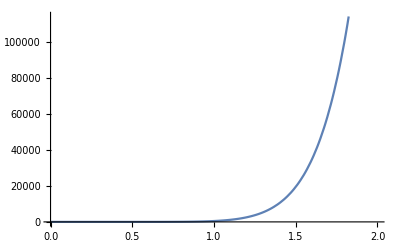

```mathematica
Ed[ξ_,nx_,nz_]:=Plot[(γ*(1+ξ)^2)/(2*w)*((1-ux[γ,ξ,nx,nz]^2)/ux[γ,ξ,nx,nz]^4),{γ,0,2}]
Ed[1,0,0]
```